# Plot thimbles and integrals

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
α=2;
f[x_,μ_]:=ⅈ((x-μ)^2+α/(1+x^2))
Block[{μ=0},
saddles=Solve[D[f[x,μ],x]==0,x];
saddlesPlot=ListPlot[ReIm[x/.saddles],PlotStyle->Red,PlotRange->{{-2,2},{-2,2}}];
thimblesPlot=ContourPlot[Im[f[u+ⅈ v,μ]]==Im[f[x,μ]/.saddles],{u,-2,2},{v,-2,2},ContourStyle->Black,PlotPoints->50];
thimblesPlot⟦1,1,2,1,3,1,2;;-1⟧=thimblesPlot⟦1,1,2,1,3,1,{1,4,5,6,9,10}⟧;
bound=RegionPlot[Re[f[u+ⅈ v,μ]]<-2,{u,-2,2},{v,-2,2},PlotPoints->50,PlotStyle->LightGray,BoundaryStyle->LightGray];
]
```

```mathematica
Manipulate[
Module[{simplices},
simplices=Partition[Partition[BinaryReadList["files/simplices"<>ToString[Floor[i]]<>".bin","Real64"],2].{1,ⅈ},2];
Show[
bound,
thimblesPlot,
Graphics[{Blue,Thick,Line[ReIm[simplices]]},PlotRange->{{-2,2},{-2,2}},Axes->True],
Graphics[{Yellow,Point[ReIm[simplices⟦All,1⟧]]}],
saddlesPlot,ImageSize->500,Axes->True
]
]
,{{i,0,"λ"},0,150,1}]
```

```mathematica
Manipulate[
Module[{simplices,files,fileν,νs,saddles,μ,ν,filesSort},
files=FileNames["files/simplices_mu=*.bin"];
fileν=Map[Flatten[{#,ToExpression[StringCases[#,"simplices_mu="~~x__~~"_nu="~~y__~~".bin"->{x,y}]]}]&,files];
νs=Union[fileν⟦All,3⟧];
filesSort=SortBy[Select[fileν,#⟦3⟧==νs⟦j⟧&],#⟦2⟧&];
μ=filesSort⟦i,2⟧;
ν=filesSort⟦i,3⟧;
simplices=Partition[Partition[BinaryReadList[filesSort⟦i,1⟧,"Real64"],2].{1,ⅈ},2];
saddles=Quiet[Solve[D[f[x,μ],x]==0,x]];
Show[
RegionPlot[Re[f[u+ⅈ v,μ]]<-2,{u,-2,2},{v,-2,2},PlotPoints->50,PlotStyle->LightGray,BoundaryStyle->LightGray,
PlotLabel->"μ = "<>ToString[μ]<>" ν = " <>ToString[ν]<>" N_s = "<>ToString[Length[simplices]]],
ListPlot[ReIm[x/.saddles],PlotStyle->Red,PlotRange->{{-2,2},{-2,2}}],
Graphics[{Blue,Thick,Line[ReIm[simplices]]},PlotRange->{{-2,2},{-2,2}},Axes->True],
Graphics[{Yellow,Point[ReIm[simplices⟦All,1⟧]]}],
ListPlot[ReIm[x/.saddles],PlotStyle->Red,PlotRange->{{-2,2},{-2,2}}],ImageSize->500,Axes->True
]
]
,{{i,9,"μ"},1,17,1},{{j,1,"ν"},1,4,1}]
```

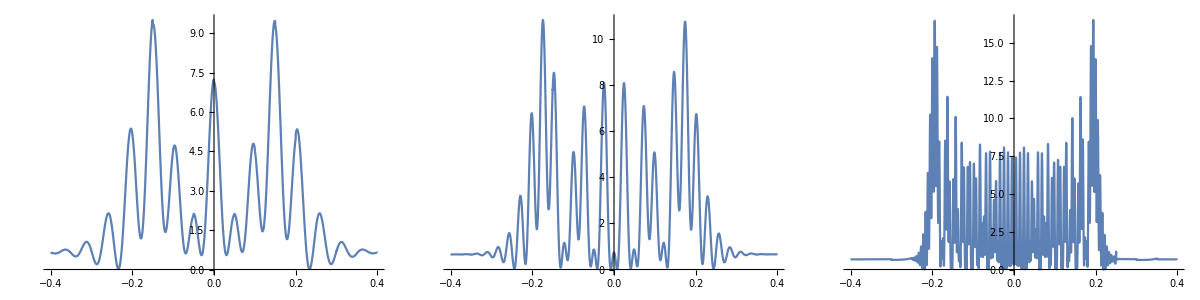

```mathematica
Module[{ψ},
Grid[{{
ψ=Partition[BinaryReadList["files/psi_nu=50.bin","Real64"],2].{1,ⅈ};
ListLinePlot[Abs[ψ]^2, DataRange->{-0.4,0.4},ImageSize->400,PlotRange->All]
,
ψ=Partition[BinaryReadList["files/psi_nu=100.bin","Real64"],2].{1,ⅈ};
ListLinePlot[Abs[ψ]^2, DataRange->{-0.4,0.4},ImageSize->400,PlotRange->All]
,
ψ=Partition[BinaryReadList["files/psi_nu=500.bin","Real64"],2].{1,ⅈ};
ListLinePlot[Abs[ψ]^2, DataRange->{-0.4,0.4},ImageSize->400,PlotRange->All]
}}]
]
```